## Fit Stellarator Surface to Ellipse

```mathematica
(*INPUT FROM VMEC*)
(*vmecInput="/Users/rogeriojorge/local/venmac/input_LHD.txt";*)
(*VMEC Output File*)
vmecOutput="/Users/rogeriojorge/Dropbox/senac/vmec/W7X/wout_W7X.nc";
```

```mathematica
(*VMEC Axis and Surface Shape*)
If[FileExistsQ[vmecOutput],
	iradius=5;
	ιAxisOut=Import[vmecOutput,{"Datasets","iotaf"}][[iradius]];
	rmnc=Import[vmecOutput,{"Datasets","rmnc"}];
	zmns=Import[vmecOutput,{"Datasets","zmns"}];
	nns=Import[vmecOutput,{"Datasets","ns"}];
	vmecNFP=Import[vmecOutput,{"Datasets","nfp"}];
	vmecPSI=Abs[Import[vmecOutput,{"Datasets","phi"}][[iradius]]];
	B0Est=Max[Import[vmecOutput,{"Datasets","bmnc"}]];
	bmnc=Import[vmecOutput,{"Datasets","bmnc"}];
	xnnyq=Import[vmecOutput,{"Datasets","xn_nyq"}];
	xmnyq=Import[vmecOutput,{"Datasets","xm_nyq"}];
	xm=Import[vmecOutput,{"Datasets","xm"}];
	xn=Import[vmecOutput,{"Datasets","xn"}];
	vmecOutputRaxis=Import[vmecOutput,{"Datasets","raxis_cc"}];
	vmecOutputZaxis=Import[vmecOutput,{"Datasets","zaxis_cs"}];
	vmecOutputnRAXIS[ϕ_]=Chop[Sum[vmecOutputRaxis[[nn]]Cos[-vmecNFP (nn-1) ϕ],{nn,1,Length[vmecOutputRaxis]}],10^-4];
	vmecOutputnZAXIS[ϕ_]=Chop[Sum[vmecOutputZaxis[[nn]]Sin[-vmecNFP(nn-1) ϕ],{nn,1,Length[vmecOutputZaxis]}],10^-4];
	closedcurvVMEC[ϕ_]={vmecOutputnRAXIS[ϕ]Cos[ϕ],vmecOutputnRAXIS[ϕ]Sin[ϕ],vmecOutputnZAXIS[ϕ]};
	RBCVMEC[θ_,ϕ_]=Sum[rmnc[[iradius,i]]Cos[xm[[i]]θ-xn[[i]]ϕ],{i,1,Length[xn]}];
	ZBSVMEC[θ_,ϕ_]=Sum[zmns[[iradius,i]]Sin[xm[[i]]θ-xn[[i]]ϕ],{i,1,Length[xn]}];
	BVMEC[θ_,ϕ_]=Chop[Sum[bmnc[[Floor[iradius],i]]*Cos[xmnyq[[i]] θ-xnnyq[[i]] ϕ],{i,1,Length[xnnyq]}],10^-8];
,
	tmaxN=40;
	vmecNFP=StringCases[StringDelete[FindList[vmecInput,"NFP"][[1]]," "],x:NumberString:>ToExpression[x]][[1]];
	vmecPSI=Abs[StringCases[StringDelete[FindList[vmecInput,"PHIEDGE"][[1]]," "],x:NumberString:>ToExpression[x]][[1]]];
	vmecRAXIS=StringSplit[FindList[vmecInput,"RAXIS"][[1]]];
	vmecZAXIS=StringSplit[FindList[vmecInput,"ZAXIS"][[1]]];
	nRAXIS[ϕ_]=Sum[Internal`StringToDouble@vmecRAXIS[[nn+3]]Cos[vmecNFP nn ϕ],{nn,0,Dimensions[vmecRAXIS][[1]]-3}];
	nZAXIS[ϕ_]=Sum[Internal`StringToDouble@vmecZAXIS[[nn+3]]Sin[vmecNFP nn ϕ],{nn,0,Dimensions[vmecZAXIS][[1]]-3}];
	closedcurvVMEC[ϕ_]={nRAXIS[ϕ]Cos[ϕ],nRAXIS[ϕ]Sin[ϕ],nZAXIS[ϕ]};
	vmecRBC=ConstantArray[0,{tmaxN,tmaxN}];
	vmecZBS=ConstantArray[0,{tmaxN,tmaxN}];
	vmecSurf=DeleteCases[Flatten[Table[StringSplit[FindList[vmecInput,"RBC("<>ToString[i]<>","<>ToString[j]<>")"][[1]]]//Quiet,{i,-tmaxN,tmaxN},{j,0,tmaxN}]],StringSplit[{}⟦1⟧]//Quiet];
Table[ToExpression[StringJoin[StringReplace[vmecSurf[[i]],{"RBC"->"vmecRBC","ZBS"->"vmecZBS","("->"[["<>ToString[Floor[tmaxN/2]]<>"+",")"->"+"<>ToString[Floor[tmaxN/2]]<>"]]","e"->"×10^("}],")"]],{i,1,Length[vmecSurf]}];
	RBCVMEC[θ_,ϕ_]=Sum[vmecRBC[[mm,nn]]Cos[(mm-Floor[tmaxN/2]) θ-vmecNFP (nn-Floor[tmaxN/2]) ϕ],{mm,1,Length[vmecRBC]},{nn,1,Length[vmecRBC]}];
	ZBSVMEC[θ_,ϕ_]=Sum[vmecZBS[[mm,nn]]Sin[(mm-Floor[tmaxN/2]) θ-vmecNFP (nn-Floor[tmaxN/2]) ϕ],{mm,1,Length[vmecRBC]},{nn,1,Length[vmecRBC]}];
]
```

```mathematica
(*imagesize1=400;
PlotOptions=Flatten[{LabelStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->30],ImageSize->imagesize1,Frame->True,AspectRatio->1}];
DensityPlot[BVMEC[θ,ϕ],{θ,0,2π},{ϕ,0,2π},FrameLabel->{"Poloidal Angle θ","Toroidal Angle ϕ"},Evaluate@PlotOptions,MaxRecursion->2,PlotPoints->30,ColorFunction->"Rainbow",PlotLegends->BarLegend[Automatic,LegendMarkerSize->imagesize1,LegendLabel->"B(θ,ϕ)"]]*)
```

```mathematica
(*VMEC Axis Frenet-Serret Frame*)
Off[Simplify::time]
curvVMEC[t_]=Chop[Norm[Cross[closedcurvVMEC'[t],closedcurvVMEC''[t]]]/Norm[closedcurvVMEC'[t]]^3,10^-6];
torsVMEC[t_]=Chop[Dot[Cross[closedcurvVMEC'[t],closedcurvVMEC''[t]],closedcurvVMEC'''[t]]/Norm[Cross[closedcurvVMEC'[t],closedcurvVMEC''[t]]]^2,10^-6];
sprimeVMEC[t_]=Chop[Simplify[Chop[ComplexExpand[Norm[closedcurvVMEC'[t]]],10^-6],TimeConstraint->0.01],10^-6];
b0VMEC[t_]=Simplify[Chop[closedcurvVMEC'[t]/sprimeVMEC[t],10^-6],TimeConstraint->0.01];
k0VMEC[t_]=Simplify[Chop[b0VMEC'[t]/sprimeVMEC[t],10^-6],TimeConstraint->0.01]/curvVMEC[t]//Re;
t0VMEC[t_]=Chop[Cross[b0VMEC[t],k0VMEC[t]],10^-6]//Re;
(*Flux Surface of VMEC*)
FluxSurfaceVMEC[θ_,ϕ_]=Simplify[Chop[{RBCVMEC[θ,ϕ] Cos[ϕ],RBCVMEC[θ,ϕ] Sin[ϕ],ZBSVMEC[θ,ϕ]},10^-6],TimeConstraint->0.01]//Re;
```

```mathematica
(*Look at VMEC Surface*)
(*Manipulate[Show[{ParametricPlot3D[FluxSurfaceVMEC[θ,ϕ],{θ,0,2π},{ϕ,0,2π},Mesh->None,PlotStyle->Directive[Opacity[0.5],Specularity[White,20]]],ParametricPlot3D[closedcurvVMEC[ϕ],{ϕ,0,2π}],Graphics3D[Dynamic@Translate[{Thick,Red,Arrow[{{0,0,0},2b0VMEC[t]}],Green,Arrow[{{0,0,0},2k0VMEC[t]}],Blue,Arrow[{{0,0,0},2t0VMEC[t]}]},closedcurvVMEC[t]]]}],{t,0,2π}]*)
```

```mathematica
ϕAxis=Interpolation[Flatten[ParallelTable[{{θ,ϕ},x/.FindRoot[Dot[b0VMEC[x],FluxSurfaceVMEC[θ,ϕ]-closedcurvVMEC[x]],{x,ϕ}]},{θ,0,2π,2π/50},{ϕ,0,2π,2π/100}],1]];
ycomponent[θ_,ϕ_]=Dot[FluxSurfaceVMEC[θ,ϕ]-closedcurvVMEC[ϕAxis[θ,ϕ]],t0VMEC[ϕAxis[θ,ϕ]]];
xcomponent[θ_,ϕ_]=Dot[FluxSurfaceVMEC[θ,ϕ]-closedcurvVMEC[ϕAxis[θ,ϕ]],k0VMEC[ϕAxis[θ,ϕ]]];
θMercierFunc[θ_,ϕ_]:=Chop[ArcTan[xcomponent[θ,ϕ],ycomponent[θ,ϕ]],10^-6];
```

```mathematica
rhoSurf[θ_,ϕ_]=FluxSurfaceVMEC[θ,ϕ]-closedcurvVMEC[ϕAxis[θ,ϕ]];
rhonVMEC2[θ_,ϕ_]=Chop[Dot[rhoSurf[θ,ϕ],k0VMEC[ϕAxis[θ,ϕ]]]^2+Dot[rhoSurf[θ,ϕ],t0VMEC[ϕAxis[θ,ϕ]]]^2,10^-6];
```

```mathematica
(*Flux Surface After Fitting for mu and delta*)
NTheta=15;
NPhi=20;
timestart=AbsoluteTime[];
counter=0;
SetSharedVariable[counter];
PrintTemporary[Dynamic["Percent Completed: "<>ToString[N[(counter*100)/((NTheta+1) (NPhi+1))]]<>"% \nTime elapsed: "<>ToString[AbsoluteTime[]-timestart]<>" s \nEstimated Time remaining: "<>ToString[(((NTheta+1) (NPhi+1)-counter) (AbsoluteTime[]-timestart))/counter]<>"s "]];
dataVMEC=Flatten[ParallelTable[counter++;{θ,ϕ,Re[√rhonVMEC2[θ,ϕ]]},{θ,0,2π,2π/NTheta},{ϕ,0, 2π/vmecNFP, 2π/vmecNFP/NPhi}],1];
```

```mathematica
nModes=2;ordern=3;deltac0=0;
Clear[psin,rhon,rho,rhoSeries,positiveRhoPos]
(*Order 0 and 1 are zero*)
psin[theta_,phi_,0]=0;
psin[theta_,phi_,1]=0;
rhon[theta_,phi_,0]=0;
(*Expression for rho of psi*)
psiSeries[rhoo_,theta_,phi_,orderN_]=Sum[psin[theta,phi,n]*rhoo^n,{n,0,orderN}];
rhoSeries[psii_,theta_,phi_,orderN_]=Sum[rhon[theta,phi,n]*psii^(n/2),{n,0,orderN-1}];
rho[theta_,phi_]=rhoSeries[psii,theta,phi,ordern]/.Solve[CoefficientList[Assuming[{rhoo>0,psii>0},Normal[Series[psiSeries[rhoSeries[psii^2,theta,phi,ordern],theta,phi,ordern],{psii,0,ordern+1}]]]-psii^2,psii][[3;;ordern+1]]==0,Flatten[Table[{rhon[theta,phi,n]},{n,1,ordern-1}]]];
positiveRhoPos=Position[Coefficient[rho[1,1]/.psii->1,1/Sqrt[psin[1,1,2]]],1][[1,1]];
rho[theta_,phi_]=rho[theta,phi][[positiveRhoPos]]/.psii->vmecPSI;
(*Order n psi*)
Table[psin[theta_,phi_,n]=((B0VMEC)^(n/2))*Sum[If[EvenQ[n],(Sum[psicc[n,2 i,j]*Cos[vmecNFP*j*phi]+psics[n,2 i,j]*Sin[vmecNFP*j*phi],{j,0,nModes}])*Cos[2 i*(theta+deltaVMEC)]+(Sum[psisc[n,2 i,j]*Cos[vmecNFP*j*phi]+psiss[n,2 i,j]*Sin[vmecNFP*j*phi],{j,0,nModes}])*Sin[2 i*(theta+deltaVMEC)],(Sum[psicc[n,2 i+1,j]*Cos[vmecNFP*j*phi]+psics[n,2 i+1,j]*Sin[vmecNFP*j*phi],{j,0,nModes}])*Cos[(2 i+1)*(theta+deltaVMEC)]+(Sum[psisc[n,2 i+1,j]*Cos[vmecNFP*j*phi]+psiss[n,2 i+1,j]*Sin[vmecNFP*j*phi],{j,0,nModes}])*Sin[(2 i+1)*(theta+deltaVMEC)]],{i,0,Floor[n/2]}],{n,0,ordern}];
(*Order 0 and 1 are zero*)
psin[theta_,phi_,0]=0;
psin[theta_,phi_,1]=0;
(*Order 2 is an ellipse*)
muVMEC=muc[0]+Sum[muc[i]*Cos[vmecNFP i phi],{i,1,nModes}];
deltaVMEC=deltal*phi/2+deltac0+Sum[deltas[i]*Sin[vmecNFP i phi],{i,1,nModes}];
B0VMEC=B0c[0]+Sum[B0c[i]*Cos[vmecNFP i phi],{i,1,nModes}];
psin[theta_,phi_,2]=Pi*(B0VMEC)*(1+muVMEC*Cos[2*(theta+deltaVMEC)])/Sqrt[1-(muVMEC)^2];
Clear[modelVMEC]
modelVMEC=Re[rho[θMercierFunc[theta,phi],ϕAxis[theta,phi]]];
```

```mathematica
fitParams=FindFit[dataVMEC,DeleteCases[Flatten[{modelVMEC,0.2<(muVMEC/.phi->0)<0.9,0.2<(muVMEC/.phi->Pi)<0.9,0.01<(B0VMEC/.phi->0),0.01<(B0VMEC/.phi->Pi),-1.2 vmecNFP≤deltal≤1.2 vmecNFP,Flatten[Table[{{-Pi<deltas[i]<Pi}},{i,1,nModes}]],If[ordern>2,Flatten[Table[Table[If[EvenQ[n],{-0.01<Sum[psics[n,2 i,j],{j,1,nModes}]<0.01,-0.01<Sum[psisc[n,2 i,j],{j,0,nModes}]<0.01},{-0.01<Sum[psics[n,2 i+1,j],{j,1,nModes}]<0.01,-0.01<Sum[psisc[n,2 i+1,j],{j,0,nModes}]<0.01}],{i,0,Floor[n/2]}],{n,ordern,ordern}],3],xa]},1],xa],DeleteCases[Flatten[{{{deltal,-5},{B0c[0],B0Est},{muc[0],0.4}},Flatten[Table[{{B0c[i],0.01*B0Est},{muc[i],0.01},{deltas[i],0.01}},{i,1,nModes}],1],If[ordern>2,Flatten[Table[Table[Table[If[EvenQ[n],If[j>0,{{psics[n,2 i,j],10},{psicc[n,2 i,j],10},{psisc[n,2 i,j],10},{psiss[n,2 i,j],10}},{{psisc[n,2 i,j],10},{psicc[n,2 i,j],10}}],If[j>0,{{psics[n,2 i+1,j],10},{psicc[n,2 i+1,j],10},{psisc[n,2 i+1,j],10},{psiss[n,2 i+1,j],10}},{{psisc[n,2 i+1,j],10},{psicc[n,2 i+1,j],10}}]],{j,0,nModes}],{i,0,Floor[n/2]}],{n,ordern,ordern}],3],xa]},1],xa],{theta,phi},Method->{"NMinimize"},MaxIterations->150,AccuracyGoal->5,PrecisionGoal->5]
rhonFitVMEC[theta_,phi_]=rho[theta,phi]/.fitParams;
```

{deltal→-0.00802544,B0c[0]→2.35118,muc[0]→0.138265,B0c[1]→0.0854736,muc[1]→0.345259,deltas[1]→0.963297,B0c[2]→0.254065,muc[2]→0.406993,deltas[2]→-0.638598,psisc[3,1,0]→-0.0410605,psicc[3,1,0]→-0.829835,psics[3,1,1]→-0.0249937,psicc[3,1,1]→-0.488331,psisc[3,1,1]→0.123831,psiss[3,1,1]→-1.061,psics[3,1,2]→0.0152428,psicc[3,1,2]→-1.6214,psisc[3,1,2]→-0.0745502,psiss[3,1,2]→-1.177,psisc[3,3,0]→-0.0175784,psicc[3,3,0]→-0.643518,psics[3,3,1]→0.0515027,psicc[3,3,1]→0.574491,psisc[3,3,1]→0.00985121,psiss[3,3,1]→1.14786,psics[3,3,2]→-0.0454303,psicc[3,3,2]→0.785885,psisc[3,3,2]→0.0140338,psiss[3,3,2]→0.438549}

```mathematica
GaussLegendreQuadrature[f_,{x_,a_,b_},n_Integer: 10,prec_: MachinePrecision]:=Module[{nodes,weights},{nodes,weights}=Most[NIntegrate`GaussRuleData[n,prec]];
(b-a) weights.Map[Function[x,f],Rescale[nodes,{0,1},{a,b}]]];
quadrant=0;nNormal=0;diffQuadrant=0;qnew=0;
Table[normalx=k0VMEC[t][[1]]*Cos[t]+k0VMEC[t][[2]]*Sin[t];
normaly=k0VMEC[t][[3]];
If[Abs[normalx]>Abs[normaly],If[normalx>0,qnew=2,qnew=4],If[normaly>0,qnew=1,qnew=3]];
If[quadrant==0,quadrant=qnew,diffQuadrant=qnew-quadrant;];
If[Abs[diffQuadrant]==3,diffQuadrant=diffQuadrant/3];nNormal=nNormal+diffQuadrant/2;
quadrant=qnew;,{t,0,2*Pi,2*Pi/vmecNFP/15}];
nNormal
ι0VMEC1=GaussLegendreQuadrature[( -D[deltaVMEC/.fitParams,phi]+ torsVMEC[phi]sprimeVMEC[phi])√(1-(muVMEC/.fitParams)^2)+  D[deltaVMEC/.fitParams,phi],{phi,0,2π},70,20]/(2π)-nNormal
ιAxisOut
```

-5

0.389332

0.858252

```mathematica
FluxSurfacenFitVMEC[ω_,s_]=Chop[closedcurvVMEC[ϕ]+(ρ[θ,ϕ]/.fitParams)(Cos[θ]k0VMEC[ϕ]+Sin[θ]t0VMEC[ϕ]),10^-6];
θMercierTable=ParallelTable[θMercierFunc[θ,ϕ],{θ,0,2π,2 π/20},{ϕ,0,1.1 2π/vmecNFP,1.1 2π/vmecNFP/20}];
θMercier=ListInterpolation[θMercierTable[[All,All]],{{0,2π},{0,2π}},Method->"Spline",InterpolationOrder->3];
RBCFit[ϕ_,θ_]=Re[Cos[ϕ]FluxSurfacenFitVMEC[θMercier[ θ,ϕ],ϕAxis[θ,ϕ]][[1]]+Sin[ϕ]FluxSurfacenFitVMEC[θMercier[ θ,ϕ],ϕAxis[θ,ϕ]][[2]]];
ZBSFit[ϕ_,θ_]=Re[FluxSurfacenFitVMEC[θMercier[ θ,ϕ],ϕAxis[θ,ϕ]][[3]]];
```

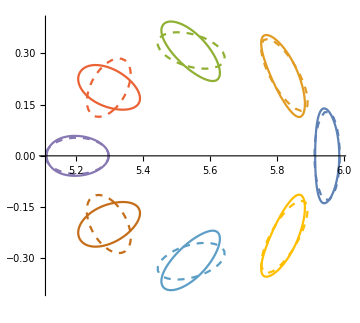

```mathematica
nPlots=8;pi=Pi;
fig2=Show[{ParametricPlot[Evaluate[{RBCFit[#,theta],ZBSFit[#,theta]}&/@Table[phi,{phi,0,2*pi/vmecNFP,2*pi/nPlots/vmecNFP}][[1;;nPlots]]],{theta,0,2*pi},PlotPoints->30,MaxRecursion->1,PlotStyle->Dashed],ParametricPlot[Evaluate[{RBCVMEC[theta,#],ZBSVMEC[theta,#]}&/@Table[phi,{phi,0,2*pi/vmecNFP,2*pi/nPlots/vmecNFP}][[1;;nPlots]]],{theta,0,2*pi},PlotPoints->30,MaxRecursion->1]},FrameLabel->{"R [meters]","Z [meters]"},PlotRange->All,ImageSize->Medium]
```

```mathematica
(*Look at results and compare with original*)
(*nPlots=4;
rangePlot={{NMinimize[{RBCVMEC[ϕ,θ],0<ϕ≤2π,0<θ≤2π},{ϕ,θ}][[1]],
NMaximize[{RBCVMEC[ϕ,θ],0<ϕ≤2π,0<θ≤2π},{ϕ,θ}][[1]]},
{NMinimize[{ZBSVMEC[ϕ,θ],0<ϕ≤2π,0<θ≤2π},{ϕ,θ}][[1]],
NMaximize[{ZBSVMEC[ϕ,θ],0<ϕ≤2π,0<θ≤2π},{ϕ,θ}][[1]]}};
ColorsPlot={Red,Purple,Green,Blue,Orange,Green,Black,Gray,Yellow,Magenta,Cyan};*)
(*Grid[{ParallelTable[ParametricPlot[{RBCFit[ϕ,θ],ZBSFit[ϕ,θ]},{θ,0,2π},PlotStyle->ColorsPlot[[1+Floor[ϕ nPlots/(2π)]]],AspectRatio->1,PlotRange->rangePlot,PlotPoints->60,MaxRecursion->1],{ϕ,0,2π,2π/nPlots}],ParallelTable[ParametricPlot[{RBCVMEC[θ,ϕ],ZBSVMEC[θ,ϕ]},{θ,0,2π},PlotStyle->ColorsPlot[[1+Floor[ϕ nPlots/(2π)]]],AspectRatio->1,PlotRange->rangePlot,PlotPoints->20,MaxRecursion->1],{ϕ,0,2π,2π/nPlots}]}]*)
Manipulate[Show[{ParametricPlot[{RBCFit[ϕ,θ],ZBSFit[ϕ,θ]},{θ,0,2π},PlotStyle->Dashed,PlotPoints->30,MaxRecursion->1],ParametricPlot[{RBCVMEC[θ,ϕ],ZBSVMEC[θ,ϕ]},{θ,0,2π},PlotPoints->30,MaxRecursion->1]},PlotRange->All],{ϕ,0,2π/vmecNFP,AnimationRate->2π/vmecNFP/10,Appearance->"Open"}]
```

```mathematica
(*VMEC File Input*)
vmecPSI
vmecNFP
vmecOutputnZAXIS[-ϕ]
vmecOutputnRAXIS[ϕ]
(*Chop[B0c[0]+ Sum[B0c[i] Cos[vmecNFP i ϕ](*+B0s[i] Sin[vmecNFP i ϕ]*),{i,1,nModes}]/.fitParams,10^-6]
Chop[muc[0]+Sum[muc[i] Cos[vmecNFP i ϕ](*+mus[i] Sin[vmecNFP i ϕ]*),{i,1,nModes}]/.fitParams,10^-6]
Chop[deltal ϕ+deltac[0]+Sum[(*deltac[i] Cos[vmecNFP i ϕ]+*)deltas[i] Sin[vmecNFP i ϕ],{i,1,nModes}]/.fitParams,10^-6]*)
```

3.23388

10

0.00778911 Sin[10 ϕ]

3.75925+0.00766231 Cos[10 ϕ]

```mathematica
maxm=6;maxn=12;
maxRecursTheta=30;maxRecursPhi=300;
```

```mathematica
timestart=AbsoluteTime[];counter=0;
PrintTemporary[Dynamic["Percent Completed: "<>ToString[N[(counter*100)/((maxm+1) (2maxn+1))]]<>"% \nTime elapsed: "<>ToString[AbsoluteTime[]-timestart]<>" s \nEstimated Time remaining: "<>ToString[(((maxm+1) (2maxn+1)-counter) (AbsoluteTime[]-timestart))/counter]]];
ParallelEvaluate[Off[NIntegrate::ncvi,NIntegrate::slwcon,NIntegrate::eincr ]];
RBCmn=Quiet[ParallelTable[counter++;GaussLegendreQuadrature[GaussLegendreQuadrature[RBCFit[ϕ,θ]Cos[mm θ-vmecNFP nn ϕ],{ϕ,0,2π},maxRecursPhi,20],{θ,0,2π},maxRecursTheta,20]/If[mm==0&&nn==0,4 π^2,2 π^2],{mm,0,maxm},{nn,-maxn,maxn}]/.Indeterminate->0.];
timestart=AbsoluteTime[];counter=0;
ZBSmn=
Quiet[ParallelTable[counter++;GaussLegendreQuadrature[GaussLegendreQuadrature[ZBSFit[ϕ,θ]Sin[mm θ-vmecNFP nn ϕ],{ϕ,0,2π},maxRecursPhi,20],{θ,0,2π},maxRecursTheta,20]/If[mm==0&&nn==0,1,2 π^2],{mm,0,maxm},{nn,-maxn,maxn}]/.Indeterminate->0.];
```

$Aborted

$Aborted

```mathematica
regcoilDatasets=Import["/Users/rogeriojorge/Dropbox/senac/vmec/LHD/regcoil_out_LHD.nc",{"Datasets",{"xm_plasma","xn_plasma","rmnc_plasma","zmns_plasma","xm_coil","xn_coil","rmnc_coil","zmns_coil","xm_potential","xn_potential","single_valued_current_potential_mn","nfp","net_poloidal_current_Amperes","net_toroidal_current_Amperes"}}];
```

```mathematica
xmplasma=regcoilDatasets[[1]];
xnplasma=regcoilDatasets[[2]];
rmncplasma=regcoilDatasets[[3]];
zmnsplasma=regcoilDatasets[[4]];
xmcoil=regcoilDatasets[[5]];
xncoil=regcoilDatasets[[6]];
rmnccoil=regcoilDatasets[[7]];
zmnscoil=regcoilDatasets[[8]];
xmpotential=regcoilDatasets[[9]];
xnpotential=regcoilDatasets[[10]];
svcurrentpotentialmn=regcoilDatasets[[11]];
nfpcoil=regcoilDatasets[[12]];
netpcurrentA=regcoilDatasets[[13]];
nettcurrentA=regcoilDatasets[[14]];
```

```mathematica
(*Input Parameters*)
coilsPerHalfPeriod=2;
numHalfPeriodsToPlot=0;If[numHalfPeriodsToPlot==0,numHalfPeriodsToPlot=nfpcoil*2];
thetaShift=0;
pi=N[Pi,10];
```

```mathematica
currentpotentialmn=svcurrentpotentialmn[[Length[svcurrentpotentialmn[[All,1]]],All]];
currentpotentialTemp[theta_,phi_]=0;
Table[angle[theta_,phi_]=xmpotential[[im]]*theta-xnpotential[[im]]*phi;currentpotentialTemp[theta_,phi_]=currentpotentialTemp[theta,phi]+currentpotentialmn[[im]]*Sin[angle[theta,phi]];,{im,1,Length[xmpotential]}];
currentpotential=Compile[{{theta,_Real},{phi,_Real}},currentpotentialTemp[theta,phi]+netpcurrentA*phi/(2*pi)+nettcurrentA*theta/(2*pi)];
```

```mathematica
minCurr=FindMinValue[{currentpotential[theta,phi],0≤theta≤2*pi&&0≤phi≤2*pi},{theta,phi}];
maxCurr=FindMaxValue[{currentpotential[theta,phi],0≤theta≤2*pi&&0≤phi≤2*pi},{theta,phi}];
coilContours=(ParallelTable[(Interpolation[ContourPlot[currentpotential[theta,phi]==i,{theta,0,2π},{phi,0,2π},PlotPoints->70,MaxRecursion->1][[1,1,1]],Method->"Spline",InterpolationOrder->2])//Quiet,{i,minCurr,maxCurr,(maxCurr-minCurr)/(coilsPerHalfPeriod*2*nfpcoil+1)}]//Quiet)[[2;;coilsPerHalfPeriod*2*nfpcoil+1]]//Quiet;
```

CompiledFunction::cfsa: Argument theta at position 1 should be a machine-size real number.

```mathematica
If[Dimensions[Position[rmncplasma,_?(10^-10<#<10^-8&)]][[1]]>3 && NumberQ[Position[rmncplasma,_?(10^-10<#<10^-8&)][[1,1]]],imMaxP=Position[rmncplasma,_?(10^-10<#<10^-8&)][[4,1]],imMaxP=Length[rmncplasma]];
plasmaposTemp[theta_,phi_]={0,0,0};
plasmaposTemp[theta_,phi_]=ParallelSum[
angle[theta_,phi_]=xmplasma[[im]]*theta-xnplasma[[im]]*phi;
{rmncplasma[[im]]*Cos[angle[theta,phi]]*Cos[phi],rmncplasma[[im]]*Cos[angle[theta,phi]]*Sin[phi],zmnsplasma[[im]]*Sin[angle[theta,phi]]},{im,1,imMaxP}];
```

```mathematica
If[Dimensions[Position[rmnccoil,_?(10^-13<#<10^-12&)]][[1]]>8 && NumberQ[Position[rmnccoil,_?(10^-13<#<10^-12&)][[1,1]]],imMax=Position[rmnccoil,_?(10^-13<#<10^-12&)][[9,1]],imMax=Length[rmnccoil]];
WSposTemp[theta_,phi_]=ParallelSum[angle[theta_,phi_]=xmcoil[[im]]*theta-xncoil[[im]]*phi;
{rmnccoil[[im]]*Cos[angle[theta,phi]]*Cos[phi],rmnccoil[[im]]*Cos[angle[theta,phi]]*Sin[phi],zmnscoil[[im]]*Sin[angle[theta,phi]]},{im,1,imMax}];
Table[coilposTemp[theta_,j]=ParallelSum[angle2[theta_]=coilContours[[j]][theta];
anglec[theta_]=xmcoil[[im]]*theta-xncoil[[im]]*angle2[theta];
{rmnccoil[[im]]*Cos[anglec[theta]]*Cos[angle2[theta]],rmnccoil[[im]]*Cos[anglec[theta]]*Sin[angle2[theta]],zmnscoil[[im]]*Sin[anglec[theta]]},{im,1,imMax}],{j,1,coilsPerHalfPeriod*numHalfPeriodsToPlot}];
```

1201

```mathematica
plasmapos[theta_,phi_]=Chop[plasmaposTemp[theta,phi],10^-7];WSpos[theta_,phi_]=Chop[WSposTemp[theta,phi],10^-7];
Table[coilpos[theta_,j]=Chop[coilposTemp[theta,j],10^-7],{j,1,coilsPerHalfPeriod*numHalfPeriodsToPlot}];
```

```mathematica
npointsCoilPos=40;
Table[
coilposTable=Table[{{theta,coilposTemp[theta,j][[1]]},{theta,coilpos[theta,j][[2]]},{theta,coilpos[theta,j][[3]]}},{theta,0,2*pi,2*pi/npointsCoilPos}];
coilposInterp={Interpolation[coilposTable[[All,1]],Method->"Spline",InterpolationOrder->2],Interpolation[coilposTable[[All,2]],Method->"Spline",InterpolationOrder->2],Interpolation[coilposTable[[All,3]],Method->"Spline",InterpolationOrder->2]};
coilposFunc[theta_,j]={coilposInterp[[1]][theta],coilposInterp[[2]][theta],coilposInterp[[3]][theta]};
,{j,1,coilsPerHalfPeriod*numHalfPeriodsToPlot}];
```

```mathematica
plasmaPlot=ParametricPlot3D[plasmapos[theta,phi],{theta,0,2*pi},{phi,0,2*pi},PlotPoints->{20,30},MaxRecursion->2,Mesh->None,PlotStyle->Directive[Opacity[0.8],Specularity[White,20]]];
(*windingPlot=ParametricPlot3D[WSpos[theta,phi],{theta,0,2*pi},{phi,0,2*pi},PlotPoints->{15,50},MaxRecursion->1,Mesh->None,PlotStyle->Directive[LightBlue,Opacity[0.3]]];*)
```

```mathematica
WSposTable=ParallelTable[{{theta,phi},WSpos[theta,phi]},{theta,0,2*pi,2*pi/npointsCoilPos},{phi,0,2*pi,2*pi/60}];
WSposInterp=Interpolation[Flatten[WSposTable,1],Method->"Spline",InterpolationOrder->3];
```

```mathematica
thickness=0.15;
regcoilPlotFig=Show[plasmaPlot,Table[
tangentTheta[theta_]= D[WSposInterp[theta,phi],theta]/.phi->coilContours[[j]][theta];
utangentTheta[theta_]=tangentTheta[theta]/Norm[tangentTheta[theta]];
tangentPhi[theta_]= D[WSposInterp[theta,phi],phi]/.phi->coilContours[[j]][theta];
utangentPhi[theta_]=tangentPhi[theta]/Norm[tangentPhi[theta]];
unormalWSpos[theta_]=Cross[utangentPhi[theta],utangentTheta[theta]];
ParametricPlot3D[{coilposFunc[theta,j]+x utangentPhi[theta],coilposFunc[theta,j]+thickness utangentPhi[theta]+x unormalWSpos[theta],coilposFunc[theta,j]+x unormalWSpos[theta],coilposFunc[theta,j]+x utangentPhi[theta]+thickness unormalWSpos[theta]},{theta,0,2Pi},{x,0,thickness},PlotPoints->{20,3},MaxRecursion->2,Mesh->None,PlotStyle->Directive[Gray,Specularity[White,20]]],{j,1,coilsPerHalfPeriod*numHalfPeriodsToPlot}],Boxed->False,ImageSize->Large,Axes->False,PlotRange->All]
(*ParametricPlot3D[WSpos[theta,phi],{theta,0,2Pi},{phi,0,2Pi},PlotPoints->{5, 8},MaxRecursion->1]*)
```

-Graphics3D-

```mathematica
Export["/Users/rogeriojorge/Dropbox/W7X_coils.png",regcoilPlotFig,ImageSize->1000,ImageResolution->500];
```

```mathematica
RBCfinal[θ_,ϕ_]=Sum[RBCmn[[mm+1,nn+maxn+1]]Cos[mm θ-vmecNFP nn ϕ],{mm,0,maxm},{nn,-maxn,maxn}];
ZBSfinal[θ_,ϕ_]=Sum[ZBSmn[[mm+1,nn+maxn+1]]Sin[mm θ-vmecNFP nn ϕ],{mm,0,maxm},{nn,-maxn,maxn}];
Grid[{{ParametricPlot3D[{RBCfinal[θ,ϕ] Cos[ϕ],RBCfinal[θ,ϕ] Sin[ϕ],ZBSfinal[θ,ϕ]},{ϕ,0,2π},{θ,0,2π},ImageSize->Medium]}}]
```

-Graphics3D-

```mathematica
printv="";
rbcs[n_,m_]:="RBC("<>ToString[n]<>","<>ToString[m]<>")=";
zbcs[n_,m_]:="  ZBS("<>ToString[n]<>","<>ToString[m]<>")=";
nl="
";
Do[If[m==0&&n<0||Chop[RBCmn[[m+1,n+maxn+1]],10^-8]==0&&Chop[ZBSmn[[m+1,n+maxn+1]],10^-8]==0,Null,
printv=printv<>rbcs[n,m]<>ToString[DecimalForm[RBCmn[[m+1,n+maxn+1]]]]<>zbcs[n,m]<>ToString[DecimalForm[ZBSmn[[m+1,n+maxn+1]]]]<>nl
],{m,0,maxm},{n,-maxn,maxn}]
printv
```

RBC(0,0)=3.75925  ZBS(0,0)=0
RBC(1,0)=0.00766231  ZBS(1,0)=0.00778911
RBC(7,0)=-0.0000000169087  ZBS(7,0)=0.0000000244151
RBC(8,0)=-0.000000121624  ZBS(8,0)=0.00000010478
RBC(9,0)=0.00000101769  ZBS(9,0)=-0.000000742817
RBC(10,0)=-0.000000884545  ZBS(10,0)=0.00000016236
RBC(11,0)=-0.0000000306252  ZBS(11,0)=0.000000120736
RBC(12,0)=0.000000201303  ZBS(12,0)=0.000000157921
RBC(-12,1)=0.00000652437  ZBS(-12,1)=0.00000703382
RBC(-11,1)=0.00000750085  ZBS(-11,1)=0.00000712051
RBC(-10,1)=0.00000855979  ZBS(-10,1)=0.00000761942
RBC(-9,1)=0.00000667648  ZBS(-9,1)=0.00000743343
RBC(-8,1)=0.0000106437  ZBS(-8,1)=0.0000104469
RBC(-7,1)=0.000010852  ZBS(-7,1)=0.0000112153
RBC(-6,1)=0.0000131839  ZBS(-6,1)=0.0000110612
RBC(-5,1)=0.00000949233  ZBS(-5,1)=0.0000230464
RBC(-4,1)=0.0000545609  ZBS(-4,1)=-0.0000385339
RBC(-3,1)=-0.000286715  ZBS(-3,1)=0.000428818
RBC(-2,1)=0.00320438  ZBS(-2,1)=-0.00369372
RBC(-1,1)=-0.0635592  ZBS(-1,1)=0.0667915
RBC(0,1)=-0.629283  ZBS(0,1)=0.609221
RBC(1,1)=0.162072  ZBS(1,1)=0.0345354
RBC(2,1)=0.00025527  ZBS(2,1)=0.0201376
RBC(3,1)=0.0011299  ZBS(3,1)=-0.00231314
RBC(4,1)=-0.000289022  ZBS(4,1)=0.000337174
RBC(5,1)=0.0000279279  ZBS(5,1)=-0.0000892268
RBC(6,1)=-0.0000286805  ZBS(6,1)=-0.00000634932
RBC(7,1)=-0.0000133734  ZBS(7,1)=-0.0000176894
RBC(8,1)=-0.0000135139  ZBS(8,1)=-0.0000126503
RBC(9,1)=-0.0000116683  ZBS(9,1)=-0.0000112804
RBC(10,1)=-0.00000932879  ZBS(10,1)=-0.0000104234
RBC(11,1)=-0.00000930876  ZBS(11,1)=-0.0000093526
RBC(12,1)=-0.00000856107  ZBS(12,1)=-0.00000851617
RBC(-12,2)=0.00000000258299  ZBS(-12,2)=-0.0000000160504
RBC(-11,2)=-0.0000001464  ZBS(-11,2)=0.000000225565
RBC(-10,2)=-0.000000153419  ZBS(-10,2)=0.000000452365
RBC(-9,2)=0.00000268049  ZBS(-9,2)=0.000000841511
RBC(-8,2)=-0.00000318656  ZBS(-8,2)=-0.00000257071
RBC(-7,2)=0.000000407357  ZBS(-7,2)=0.000000319927
RBC(-6,2)=0.0000000495571  ZBS(-6,2)=0.0000000633183
RBC(-5,2)=-0.00000000836972  ZBS(-5,2)=-0.0000000116637
RBC(8,2)=0.0000000127915  ZBS(8,2)=-0.0000000265595
RBC(9,2)=0.0000000463301  ZBS(9,2)=-0.0000000708935
RBC(10,2)=-0.000000560038  ZBS(10,2)=0.000000167785
RBC(11,2)=0.000000563215  ZBS(11,2)=0.00000024817
RBC(12,2)=0.000000262117  ZBS(12,2)=0.0000000104912
RBC(-12,3)=0.00000380884  ZBS(-12,3)=-0.00000972265
RBC(-11,3)=0.00000441786  ZBS(-11,3)=-0.0000107507
RBC(-10,3)=0.00000470275  ZBS(-10,3)=-0.0000112561
RBC(-9,3)=0.00000350055  ZBS(-9,3)=-0.0000116694
RBC(-8,3)=0.0000129778  ZBS(-8,3)=-0.00000953819
RBC(-7,3)=0.00000391855  ZBS(-7,3)=-0.0000185024
RBC(-6,3)=0.00000794979  ZBS(-6,3)=-0.00001839
RBC(-5,3)=0.00000943646  ZBS(-5,3)=-0.0000209438
RBC(-4,3)=0.0000123665  ZBS(-4,3)=-0.0000268841
RBC(-3,3)=0.000010071  ZBS(-3,3)=-0.0000220106
RBC(-2,3)=0.0000666241  ZBS(-2,3)=-0.000110228
RBC(-1,3)=-0.000445566  ZBS(-1,3)=0.00054759
RBC(0,3)=0.0100387  ZBS(0,3)=-0.0108196
RBC(1,3)=0.100621  ZBS(1,3)=-0.0959291
RBC(2,3)=-0.0334188  ZBS(2,3)=-0.0129916
RBC(3,3)=-0.000851874  ZBS(3,3)=-0.00393095
RBC(4,3)=-0.000149676  ZBS(4,3)=0.000454009
RBC(5,3)=0.000030044  ZBS(5,3)=-0.0000266171
RBC(6,3)=-0.0000138346  ZBS(6,3)=0.0000393979
RBC(7,3)=-0.00000421569  ZBS(7,3)=0.0000212377
RBC(8,3)=-0.00000553485  ZBS(8,3)=0.0000201128
RBC(9,3)=-0.00000469936  ZBS(9,3)=0.0000170288
RBC(10,3)=-0.00000411589  ZBS(10,3)=0.0000150014
RBC(11,3)=-0.00000493413  ZBS(11,3)=0.0000133048
RBC(12,3)=-0.00000353141  ZBS(12,3)=0.000012812
RBC(-12,4)=0.0000000171127  ZBS(-12,4)=0.0000000112102
RBC(-11,4)=0.000000113235  ZBS(-11,4)=-0.0000000258943
RBC(-10,4)=0.000000331631  ZBS(-10,4)=-0.000000667679
RBC(-9,4)=0.000000593925  ZBS(-9,4)=-0.00000153051
RBC(-8,4)=-0.00000898272  ZBS(-8,4)=-0.00000293642
RBC(-7,4)=0.0000107929  ZBS(-7,4)=0.00000878984
RBC(-6,4)=-0.00000141305  ZBS(-6,4)=-0.00000110593
RBC(-5,4)=-0.000000167476  ZBS(-5,4)=-0.000000211237
RBC(-4,4)=0.0000000294368  ZBS(-4,4)=0.0000000397356
RBC(8,4)=-0.0000000131973  ZBS(8,4)=0.00000000546727
RBC(9,4)=-0.000000029669  ZBS(9,4)=0.0000000722873
RBC(10,4)=-0.0000000493457  ZBS(10,4)=0.000000154021
RBC(11,4)=0.00000103591  ZBS(11,4)=0.000000125954
RBC(12,4)=-0.00000119427  ZBS(12,4)=-0.00000108365
RBC(-12,5)=-0.0000020872  ZBS(-12,5)=0.00000442904
RBC(-11,5)=-0.00000201042  ZBS(-11,5)=0.00000433096
RBC(-10,5)=-0.00000233955  ZBS(-10,5)=0.00000459524
RBC(-9,5)=-0.00000232583  ZBS(-9,5)=0.00000369869
RBC(-8,5)=0.00000336118  ZBS(-8,5)=0.00000169409
RBC(-7,5)=-0.0000269254  ZBS(-7,5)=-0.00000983383
RBC(-6,5)=0.00000644265  ZBS(-6,5)=0.0000157258
RBC(-5,5)=-0.00000415898  ZBS(-5,5)=0.00000843564
RBC(-4,5)=-0.000005087  ZBS(-4,5)=0.00000929172
RBC(-3,5)=-0.00000621244  ZBS(-3,5)=0.0000118025
RBC(-2,5)=-0.00000669261  ZBS(-2,5)=0.000011925
RBC(-1,5)=-0.0000213205  ZBS(-1,5)=0.0000353421
RBC(0,5)=0.0000936248  ZBS(0,5)=-0.000116809
RBC(1,5)=-0.00237678  ZBS(1,5)=0.0025858
RBC(2,5)=-0.0237976  ZBS(2,5)=0.0225816
RBC(3,5)=0.00850384  ZBS(3,5)=0.00363938
RBC(4,5)=0.000266314  ZBS(4,5)=0.000974868
RBC(5,5)=0.0000350062  ZBS(5,5)=-0.000120976
RBC(6,5)=-0.00000404586  ZBS(6,5)=-0.000000766513
RBC(7,5)=0.00000557103  ZBS(7,5)=-0.0000151688
RBC(8,5)=0.00000304552  ZBS(8,5)=-0.00000979382
RBC(9,5)=0.00000312194  ZBS(9,5)=-0.00000880775
RBC(10,5)=0.00000271194  ZBS(10,5)=-0.00000744023
RBC(11,5)=0.00000184944  ZBS(11,5)=-0.00000634329
RBC(12,5)=0.00000484385  ZBS(12,5)=-0.00000469656
RBC(-12,6)=0.0000000287368  ZBS(-12,6)=-0.0000000178694
RBC(-11,6)=-0.000000042438  ZBS(-11,6)=-0.0000000508204
RBC(-10,6)=-0.000000417413  ZBS(-10,6)=0.000000111885
RBC(-9,6)=-0.00000106596  ZBS(-9,6)=0.00000222867
RBC(-8,6)=-0.0000020352  ZBS(-8,6)=0.00000515193
RBC(-7,6)=0.0000305923  ZBS(-7,6)=0.0000100438
RBC(-6,6)=-0.0000371428  ZBS(-6,6)=-0.0000302892
RBC(-5,6)=0.00000498423  ZBS(-5,6)=0.00000392576
RBC(-4,6)=0.000000578198  ZBS(-4,6)=0.000000729119
RBC(-3,6)=-0.000000101287  ZBS(-3,6)=-0.000000135432
RBC(-1,6)=-0.00000000659863  ZBS(-1,6)=-0.000000011468
RBC(9,6)=0.0000000449221  ZBS(9,6)=-0.0000000187597
RBC(10,6)=0.0000000950878  ZBS(10,6)=-0.000000237017
RBC(11,6)=0.000000134792  ZBS(11,6)=-0.000000487458
RBC(12,6)=-0.00000325956  ZBS(12,6)=-0.000000631429

-0.331224

-0.61845